# Caminatas en 2D

Amado Cabrera

## Parámetros de inicialización

### Tamaños de los espacios de Hilbert

```mathematica
sizeP=5;
sizeC=2;
```

### Rotación de las monedas

```mathematica
α=π/4;
```

## Definiciones preliminares

### Contenido externo

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Bases de los espacios de Hiblert

```mathematica
baseP=IdentityMatrix[sizeP];
baseC=IdentityMatrix[sizeC];
```

### Funciones Ket y Bra

```mathematica
bra[n_Integer,c_Integer]:=KroneckerProduct[{baseP[[n+1]]},{baseC[[c+1]]}]
ket[n_Integer,c_Integer]:=ConjugateTranspose[bra[n,c]]
```

### Operadores

```mathematica
coin1={{Cos[α],Sin[α]},{-Sin[α],Cos[α]}};
shiftV=Sum[ket[n+1,0].bra[n,0],{n,0,sizeP-1-1}]+Sum[ket[n,1].bra[n,1],{n,0,sizeP-1}];
unitary=shiftV.KroneckerProduct[baseP,coin1];
```

```mathematica
projC=Table[
Sum[ket[n,c].bra[n,c],{n,0,sizeP-1}],{c,0,1}
];
```

```mathematica
projP=Table[
Sum[ket[n,c].bra[n,c],{c,0,1}],{n,0,sizeP-1}
];
```

### Funciones de evolución

```mathematica
DTQW[state_,step_Integer]:=Nest[unitary.#&,N[state],step]
```

```mathematica
DTQWwD[state_,step_Integer,{wc_?NumericQ,wp_?NumericQ}]:=Nest[
(1-wc-wp)unitary.#.unitary†+wc Sum[proj.unitary.#.unitary†.proj,{proj,projC}]+wp Sum[proj.unitary.#.unitary†.proj,{proj,projP}]&,
N[state],
step
];
```

## Ejemplo de caminata

### Caminata cuántica sin decoherencia

#### Caminata cuántica

```mathematica
state=#.#†&@DTQW[ket[0,0],5];
```

#### Validación del estado

```mathematica
And[0.9<Abs[Tr[state]]<1.1,PositiveSemidefiniteMatrixQ[state]]
```

True

#### Matriz de densidad reducida

```mathematica
pos=MatrixPartialTrace[state,2,{sizeP,2}];
```

#### Distribución de probabilidad

```mathematica
space=Diagonal[pos];
```

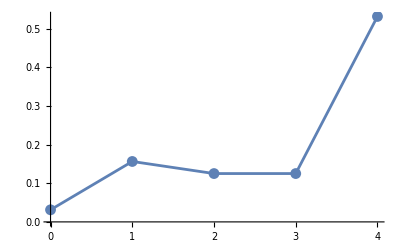

```mathematica
ListLinePlot[{Range[0,sizeP-1],space}ᵀ,
Mesh->All
]
```

### Caminata cuántica con decoherencia

#### w = 0

```mathematica
statewD=DTQWwD[ket[0,0].bra[0,0],5,{0,0}];
And[0.9<Abs[Tr[statewD]]<1.1,PositiveSemidefiniteMatrixQ[statewD]]
```

True

```mathematica
spacewD=Diagonal@MatrixPartialTrace[statewD,2,{sizeP,2}];
ListLinePlot[{Range[0,sizeP-1],spacewD}ᵀ,
Mesh->All
]
```

-Graphics-

#### wc = 1

```mathematica
statewD1=DTQWwD[ket[0,0].bra[0,0],5,{1,0}];
And[0.9<Abs[Tr[statewD1]]<1.1,PositiveSemidefiniteMatrixQ[statewD1]]
```

True

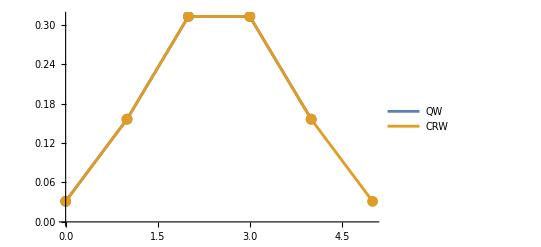

```mathematica
spacewD1=Diagonal@MatrixPartialTrace[statewD1,2,{sizeP,2}];
ListLinePlot[{{Range[0,sizeP-1],spacewD1}ᵀ,{Range[0,#],Binomial[#,Range[0,#]]/2^#}ᵀ&@5},
Mesh->All,
PlotLegends->{"QW","CRW"}
]
```

#### wp = 1

```mathematica
statewD2=DTQWwD[ket[0,0].bra[0,0],5,{0,1}];
And[0.9<Abs[Tr[statewD2]]<1.1,PositiveSemidefiniteMatrixQ[statewD2]]
```

True

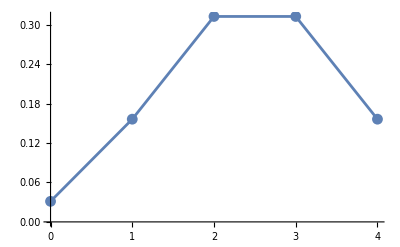

```mathematica
spacewD2=Diagonal@MatrixPartialTrace[statewD2,2,{sizeP,2}];
ListLinePlot[{Range[0,sizeP-1],spacewD2}ᵀ,
Mesh->All
]
```

#### wc = 0.5, wp = 0.5

```mathematica
statewD3=DTQWwD[ket[0,0].bra[0,0],5,{0.5,0.5}];
And[0.9<Abs[Tr[statewD3]]<1.1,PositiveSemidefiniteMatrixQ[statewD3]]
```

True

```mathematica
spacewD3=Diagonal@MatrixPartialTrace[statewD3,2,{sizeP,2}];
ListLinePlot[{Range[0,sizeP-1],spacewD3}ᵀ,
Mesh->All
]
```

-Graphics-

```mathematica
ket[4,0]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{1},{0}}

```mathematica
Sum[ket[n+2,0].bra[n,0],{n,0,sizeP-1-2}]+Sum[ket[n+1,1].bra[n,1],{n,0,sizeP-1-1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
Sum[ket[n+1,0].bra[n,0],{n,0,sizeP-1-1}]+Sum[ket[n+2,0].bra[n,0],{n,0,sizeP-1-2}]+Sum[ket[n,1].bra[n,1],{n,0,sizeP-1-0}]+Sum[ket[n+1,1].bra[n,1],{n,0,sizeP-1-1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1)